## Addendum Figures for Berry's Construction

Nicholas Wheeler
March 2018

### Figure 12a

```mathematica
r[n_]:=√(2π(n-1/8))
th[n_]:=π/4+Log[r[n] √(2π)]/(2 r[n]^2)
z[n_]:=r[n]Exp[ⅈ th[n]]

N[Table[{n,z[n]},{n,1,7}]]//TableForm
```

1. | 1.37061+1.90242 ⅈ
2. | 2.19553+2.6383 ⅈ
3. | 2.80223+3.19557 ⅈ
4. | 3.30429+3.66456 ⅈ
5. | 3.74191+4.07782 ⅈ
6. | 4.13479+4.45166 ⅈ
7. | 4.49428+4.79566 ⅈ

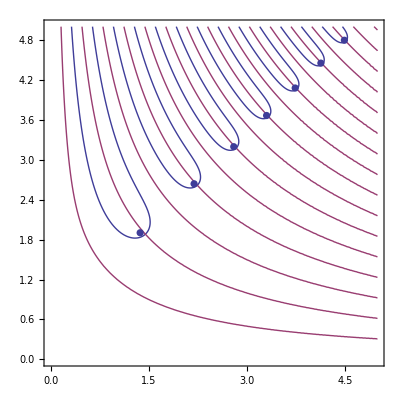

```mathematica
BerryZeros=ListPlot[{{1.37061,1.90242},{2.19553,2.6383},{2.80223,3.19557},{3.30429,3.66456},{3.74191,4.07782},{4.13479,4.45166},{4.49428,4.79566}},PlotRange->{{0,5},{0,5}},PlotStyle->{PointSize[0.013]}];

NullCurves=ContourPlot[{Re[Erf[x+ⅈ y]]==0,Im[Erf[x+ⅈ y]]==0},{x,0,5},{y,0,5},PlotPoints->50];

Show[NullCurves,BerryZeros]
```

### Figure 12b

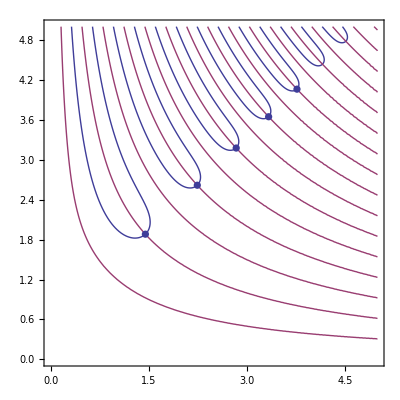

```mathematica
ExactZeros=ListPlot[{{1.45062,1.88094},{2.24466,2.61658},{2.83974,3.17563},{3.33546,3.64617},{3.76901,4.06070}},PlotRange->{{0,5},{0,5}},PlotStyle->{PointSize[0.013]}];
Show[NullCurves,ExactZeros]
```

### Figure 13a

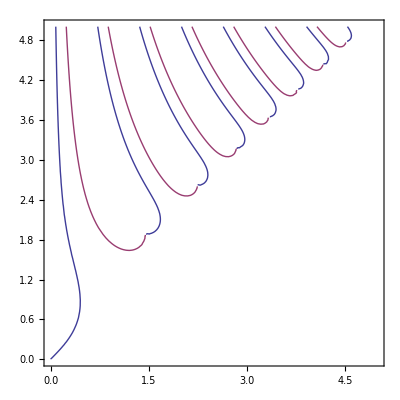

```mathematica
antiStokes=ContourPlot[{Arg[N[Erf[x+ⅈ y]]]==π/4,Arg[N[Erf[x+ⅈ y]]]==-π/4},{x,0,5},{y,0,5}]
```

### Figure 13b

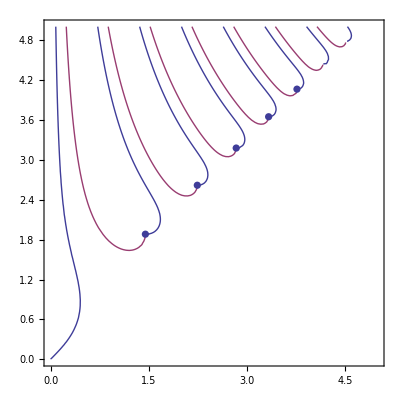

```mathematica
Show[antiStokes, ExactZeros]
```

### Figure 13c

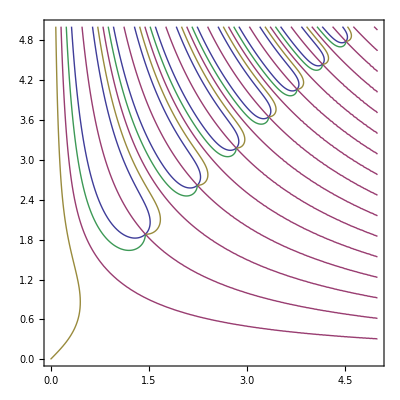

```mathematica
NullAndStokes=ContourPlot[{Re[Erf[x+ⅈ y]]==0,Im[Erf[x+ⅈ y]]==0,Arg[N[Erf[x+ⅈ y]]]==π/4,Arg[N[Erf[x+ⅈ y]]]==-π/4},{x,0,5},{y,0,5},PlotPoints->50]
```

### Figure 14

```mathematica
Plot3D[Arg[N[Erf[x+ⅈ y]]],{x,0,5},{y,0,5},PlotRange->{{0,5},{0,5},{-π,π}},Ticks->{{0,5},{0,5},{-π,π}}]
```

-Graphics3D-